Preamble

```mathematica
AppendTo[$Path,"C:\\Users\\Nilo\\__DATA\\Mega\\DATA\\eclipse-workspace2\\NumberTheory"];
<<NumberTheory`
```

```mathematica
(* NumberTheory Package Test *)
Table[{n,n^2,n^3},{n,1,6}]//tf
Sum[n^3,{n,1,6}]
nFaulhaber[3,6]
Select[nCollatz[27],OddQ]
```

1 | 1 | 1
2 | 4 | 8
3 | 9 | 27
4 | 16 | 64
5 | 25 | 125
6 | 36 | 216

441

441

{27,41,31,47,71,107,161,121,91,137,103,155,233,175,263,395,593,445,167,251,377,283,425,319,479,719,1079,1619,2429,911,1367,2051,3077,577,433,325,61,23,35,53,5,1}

## Queue MMa.SE Questions

https://math.stackexchange.com/questions/136417/what-is-so-interesting-about-the-zeroes-of-the-riemann-zeta-function/136488#136488

### Q.1

```mathematica
DirichletConvolve[1,u[n],n,m]//FullForm
```

DivisorSum[m,Function[u[Slot[1]]]]

### Q.2

```mathematica
DirichletTransform[Abs[MoebiusMu[n]],n,s]
```

Zeta[s]/Zeta[2 s]

```mathematica
DirichletTransform[MoebiusMu[n]^2,n,s]
```

DirichletTransform[MoebiusMu[n]^2,n,s]

```mathematica
Table[{k,Abs[MoebiusMu[k]],MoebiusMu[k]^2},{k,1,6}]//tf
```

1 | 1 | 1
2 | 1 | 1
3 | 1 | 1
4 | 0 | 0
5 | 1 | 1
6 | 1 | 1

## Topic

### Definition / Theorem

This is text.

#### Example

# Notes Apostol MFDSNT

1. Elliptic Functions

## 1.1 - 1.4 Elliptic functions

### Definition

A function f is called elliptic if it has the following two properties :
- f is doubly periodic;
- f is meromorphic (its only singularities in the finite plane are poles).

### Theorem 1.3

A non-constant elliptic function has a fundamental pair of periods.

#### Proof

=TBD=

### Theorem 1.4

If an elliptic function f has no poles in some period parallelogram, then f is constant.

#### Proof

=TBD=

### Theorem 1.5

If an elliptic function f has no zeros in some period parallelogram, then f is constant.

#### Proof

=TBD=

### Theorem 1.6

The contour integral of an elliptic function taken along the boundary of any cell is zero.

#### Proof

=TBD=

### Theorem 1.7

The sum of the residues of an elliptic function at its poles in any period parallelogram is zero.

#### Proof

=TBD=

### Theorem 1.8

The number of zeros of an elliptic function in any period parallelogram is equal to the number of poles, each counted with multiplicity.

#### Proof

=TBD=

## 1.5 Construction of elliptic functions

## 1.6 The Weierstrass P Function

### Weierstrass Function

```mathematica
w1=1;
w2=I;
p[z_]:=WeierstrassP[z,WeierstrassInvariants[{w1,w2}]]
```

```mathematica
ComplexPlot3D[p[z],{z,-(2w1+2w2),(2w1+2w2)}]
```

-Graphics3D-

```mathematica
ComplexPlot[p[z],{z,0,2w1+2w2},Frame->False]
```

-Graphics-

```mathematica
ComplexPlot[p[z]^15+p[z]^10+p[z]^5+p[z],{z,-(2w1+2w2),2w1+2w2},Frame->False]
```

-Graphics-

#### Some other graphs

-Graphics--Graphics--Graphics-

-Graphics--Graphics--Graphics-

### Derivative of Weierstrass Function

```mathematica
w1=1;
w2=I;
p1[z_]:=WeierstrassPPrime[z,WeierstrassInvariants[{w1,w2}]]
```

```mathematica
ComplexPlot3D[p1[z],{z,-(2w1+2w2),(2w1+2w2)}]
```

-Graphics3D-

```mathematica
ComplexPlot[p1[z],{z,-(2w1+2w2),(2w1+2w2)}]
```

-Graphics-

#### Zeros of the derivative of the Weierstrass Function

```mathematica
WeierstrassPPrime[3,WeierstrassInvariants[{w1,w2}]]//N//Chop
WeierstrassPPrime[3I,WeierstrassInvariants[{w1,w2}]]//N//Chop
WeierstrassPPrime[2+3I,WeierstrassInvariants[{w1,w2}]]//N//Chop
```

0

0

0

## 1.7 The Laurent expansion of the Weierstrass function

### Laurent Series WeierstrassP

```mathematica
1+√-3/2//N
```

1.+0.866025 ⅈ

```mathematica
Series[WeierstrassP[z,WeierstrassInvariants[{1,(1+√-3)/2}]],{z,0,18}]
```

1/z^2+(Gamma[1/3]^18 z^4)/(114688 π^6)+(Gamma[1/3]^36 z^10)/(170993385472 π^12)+(Gamma[1/3]^54 z^16)/(372606898467241984 π^18)+O[z]^19

```mathematica
Series[WeierstrassP[z,WeierstrassInvariants[{1,1+I}]],{z,0,18}]
```

1/z^2+(Gamma[1/4]^8 z^2)/(5120 π^2)+(Gamma[1/4]^16 z^6)/(78643200 π^4)+(Gamma[1/4]^24 z^10)/(2617245696000 π^6)+(Gamma[1/4]^32 z^14)/(91122026151936000 π^8)+(Gamma[1/4]^40 z^18)/(3499085804234342400000 π^10)+O[z]^19

```mathematica
Series[WeierstrassP[z,WeierstrassInvariants[{1,I}]],{z,0,18}]//N//Chop//Normal
```

1./z^2+0.590852 z^2+0.116369 z^6+0.010578 z^10+0.00091912 z^14+0.0000724085 z^18

```mathematica
p[z_]:=WeierstrassP[z,WeierstrassInvariants[{1,I}]]
q[z_]:=Series[WeierstrassP[z,WeierstrassInvariants[{1,I}]],{x,0,18}]//Normal  /. x->z
```

SetDelayed::write: Tag Complex in (-0.5-0.866025 ⅈ)[z_] is Protected.

$Failed

```mathematica
p[0.35+0.213I]
q[0.35+0.213I]
```

2.78211-5.20297 ⅈ

2.78211-5.20297 ⅈ

```mathematica
p[z_]:=WeierstrassP[z,WeierstrassInvariants[{1,(1+√-3)/2}]]
q[z_]:=Series[WeierstrassP[z,WeierstrassInvariants[{1,(1+√-3)/2}]],{x,0,18}]//Normal  /. x->z
```

SetDelayed::write: Tag Complex in (-0.5-0.866025 ⅈ)[z_] is Protected.

$Failed

## 1.8 Differential equation satisfied by the Weierstrass function

### DE-1

```mathematica
DSolve[{y'[x]^2==4 y[x]^3-a y[x]-b}, y[x], x]
```

{{y[x]→WeierstrassP[x-C[1],{a,b}]},{y[x]→WeierstrassP[x+C[1],{a,b}]}}

### DE-2

```mathematica
DSolve[{y''[x]==6 y[x]^2-1/2 b}, y[x], x]
```

{{y[x]→WeierstrassP[x+C[1],{b,C[2]}]}}

### DE-3

Note: WeierstrassZeta is NOT Elliptic, yet quasi-periodic.

```mathematica
DSolve[f'[x]==-WeierstrassP[x,WeierstrassInvariants[{1,I}]],f[x],x]
WeierstrassInvariants[{1,I}]
```

{{f[x]→C[1]+WeierstrassZeta[x,{Gamma[1/4]^8/(256 π^2),0}]}}

{Gamma[1/4]^8/(256 π^2),0}

### DE-4

Note: WeierstrassSigma is NOT Elliptic, yet entire.

```mathematica
DSolve[f'[x]==f[x] WeierstrassZeta[x,WeierstrassInvariants[{1,I}]],f[x],x]
```

{{f[x]→C[1] WeierstrassSigma[x,{Gamma[1/4]^8/(256 π^2),0}]}}

## 1.9 The Eisenstein series and the invariants g2 and g3

### Eisenstein series

```mathematica
SetAttributes[EisensteinE,{Listable,NHoldFirst}];
EisensteinE[4,q_]:=(EllipticTheta[2,0,q]^8+EllipticTheta[3,0,q]^8+EllipticTheta[4,0,q]^8)/2
EisensteinE[6,q_]:=With[{q2=EllipticTheta[2,0,q]^4,q3=EllipticTheta[3,0,q]^4,q4=EllipticTheta[4,0,q]^4},(q2+q3) (q3+q4) (q4-q2)/2]
(*
EisensteinE[n_Integer?EvenQ,q_]/;n>2:=(6/((6-n) (n^2-1) BernoulliB[n]))
Sum[Binomial[n,2 k+4] (2 k+3) (n-2 k-5) BernoulliB[2 k+4] BernoulliB[n-2 k-4] EisensteinE[2 k+4,q] EisensteinE[n-2 k-4,q],{k,0,n/2-4}]
*)
```

```mathematica
(*"equianharmonic case"*){ω1,ω3}={1,(1+I Sqrt[3])/2};
N[WeierstrassInvariants[{ω1,ω3}]]//Quiet//Chop
2 {60,140} Zeta[{4,6}] EisensteinE[{4,6},Exp[I π ω3/ω1]]/(2 ω1)^{4,6}//N//Chop
```

{0,12.8254}

{0,12.8254}

```mathematica
(*"lemniscatic case"*){ω1,ω3}={1,I};
N[WeierstrassInvariants[{ω1,ω3}]]//Quiet//Chop
2 {60,140} Zeta[{4,6}] EisensteinE[{4,6},Exp[I π ω3/ω1]]/(2 ω1)^{4,6}//N//Chop
```

{11.817,0}

{11.817,0}

```mathematica
EisensteinE[n_Integer?EvenQ,q_]/;n>2:=(6/((6-n) (n^2-1) BernoulliB[n])) Sum[Binomial[n,2 k+4] (2 k+3) (n-2 k-5) BernoulliB[2 k+4] BernoulliB[n-2 k-4] EisensteinE[2 k+4,q] EisensteinE[n-2 k-4,q],{k,0,n/2-4}]
```

```mathematica
EisensteinE[8,Exp[I π ω3/ω1]]//N//Chop
```

2.11925

```mathematica
{ω1,ω3}={1,(I)};
N[WeierstrassInvariants[{ω1,ω3}]]//Quiet//Chop
2 60Zeta[4]EisensteinE[4,Exp[I π ω3/ω1]]/(2ω1)^4//N//Chop
```

{11.817,0}

11.817

```mathematica
EisensteinE[4,Exp[I π ω3/ω1]]^2//N
EisensteinE[8,Exp[I π ω3/ω1]]//N
```

2.11925

2.11925

```mathematica
2 60 Zeta[4] EisensteinE[4,Exp[I π ω3/ω1]]/(2 ω1)^4//N//Chop
```

11.817

```mathematica
WeierstrassHalfPeriods[{11.817045008077129,0}]//N//Chop
```

{1.,0.+1. ⅈ}

```mathematica
Zeta[4]
```

π^4/90

### Testing...

```mathematica
{ω1,ω3}={1,2I};
2 60Zeta[4]EisensteinE[4,Exp[I π ω3/ω1]]/(2ω1)^4//N//Chop
π^4/12 EisensteinE[4,Exp[-π]]//N//Chop;
```

8.12422

```mathematica
WeierstrassHalfPeriods[WeierstrassInvariants[{1.07906627300369+0. ⅈ,0.5395331365018451+0.93449880478819 ⅈ}]]//N
WeierstrassHalfPeriods[WeierstrassInvariants[{ω1,ω3}]]//N
WeierstrassHalfPeriods[{0,8.124218443053023}]//N
```

{1.07907-1.10371×10^-16 ⅈ,-0.539533+0.934499 ⅈ}

{1.,0.+2. ⅈ}

{1.07907+0. ⅈ,0.539533+0.934499 ⅈ}

```mathematica
ClearAll[f]
DSolve[f''[x]==6 f[x]^2-1/2 g2,f[x],x]
```

{{f[x]→WeierstrassP[x+C[1],{g2,C[2]}]}}

```mathematica
Sum[Exp[-(n/10)^2],{n,1,Infinity}]//N
5 √π-1/2//N
```

8.36227

8.36227

### The invariants g2 and g3

## 1.10 The numbers e1, e2 and e3

```mathematica
p[z_]:=WeierstrassP[z,WeierstrassInvariants[{1,1I}]]
p[1]//N
p[I]//N
p[1+I]//N
p[z_]:=WeierstrassP[z,WeierstrassInvariants[{4,2I}]]
p[4]//N
p[2I]//N
p[4+2I]//N
```

1.7188

-1.7188

-6.66134×10^-16+3.69779×10^-32 ⅈ

0.21485+0. ⅈ

-0.411268+0. ⅈ

0.196418+2.46519×10^-31 ⅈ

```mathematica
WeierstrassP[WeierstrassHalfPeriodW1[{g2,g3}],{g2,g3}]
WeierstrassP[1,WeierstrassInvariants[{1,1I}]]
WeierstrassP[I,WeierstrassInvariants[{1,1I}]]
WeierstrassHalfPeriods[{Gamma[1/4]^4/(32 π),-Gamma[1/4]^4/(32 π)}]//N
```

WeierstrassE1[{g2,g3}]

Gamma[1/4]^4/(32 π)

-Gamma[1/4]^4/(32 π)

{0.-1.29443 ⅈ,1.31184-0.647215 ⅈ}

## 1.11 The discrimant

## 1.12 Klein’s modular function J

### Klein J

```mathematica
KleinInvariantJ[I]//N
```

1.

```mathematica
g2=WeierstrassInvariantG2[{1,I}];
g3=WeierstrassInvariantG3[{1,I}];
g2^3/(g2^3-27 g3^2)//N
```

1.

## 1.13 Invariance of J under unimodular transformations

## 1.14 The Fourier expansions of g2 and g3

## 1.15 The Fourier expansions of D and J

## Exercises

### MFDS 1.1

#### Try-out’s

```mathematica
Table[circle[0,a]//Chop,{a,0,1,0.1}]//tf
```

circle[0,0]
circle[0,0.1]
circle[0,0.2]
circle[0,0.3]
circle[0,0.4]
circle[0,0.5]
circle[0,0.6]
circle[0,0.7]
circle[0,0.8]
circle[0,0.9]
circle[0,1.]

```mathematica
circle1[u_,v_]:={(4+7/2 Cos[2 Pi u]),7/2 Sin[2 Pi u],v}
circle2[u_,v_]:={(4+7/2 Cos[2 Pi u]),7/2 Sin[2 Pi u],v}

circlePlot1=ParametricPlot3D[circle1[u,0],{u,0,1},
Mesh->5,BoundaryStyle->Black,PlotStyle->FaceForm[Red,Yellow],AxesLabel->Thread@Text[{"X","Y","Z"}]];
circlePlot2=ParametricPlot3D[circle2[u,1.0],{u,0,1},
Mesh->5,BoundaryStyle->Black,PlotStyle->FaceForm[Red,Yellow],AxesLabel->Thread@Text[{"X","Y","Z"}]];

pointPlot=Graphics3D[{Red,PointSize[0.025],Point[{4,0,0}]}];

Show[circlePlot1,circlePlot2,pointPlot,PlotRange->{{-5,8},{-5,5},{-5,5}}]
```

-Graphics3D-

```mathematica
ClearAll[x,y,z,r,θ]
data=CoordinateTransformData[];
```

```mathematica
CoordinateTransformData["Cylindrical" -> "Cartesian","Mapping", {r,θ,z}]
CoordinateTransformData["Cartesian" -> "Cylindrical","Mapping", {x,y,z}]
```

{r Cos[θ],r Sin[θ],z}

{√(x^2+y^2),ArcTan[x,y],z}

```mathematica
Det[{{1,3},{4,5}}]
Det[Transpose[{{1,3},{4,5}}]]
Det[Transpose[{{1,4},{3,5}}]]
```

-7

-7

-7

#### Answer

```mathematica
ClearAll[torus]
torus[u_,v_]:={(1+1/2 Cos[2 Pi v])Cos[2 Pi u],(1+1/2 Cos[2 Pi v])Sin[2 Pi u],1/2 Sin[2 Pi v]}
torus[u_,v_]:={(2+Cos[2 Pi v])Cos[2 Pi u],(2+Cos[2 Pi v])Sin[2 Pi u],Sin[2 Pi v]}

torusPLot=ParametricPlot3D[torus[u,v],{u,0,1},{v,0,1},
Mesh->5,BoundaryStyle->Black,PlotStyle->FaceForm[Red,Yellow],AxesLabel->Thread@Text[{"X","Y","Z"}]];
knotPlot1=ParametricPlot3D[torus[u,0],{u,0,1},AxesLabel->Thread@Text[{"X","Y","Z"}]];
knotPlot2=ParametricPlot3D[torus[0,u],{u,0,1},AxesLabel->Thread@Text[{"X","Y","Z"}]];

Show[torusPLot]
Show[knotPlot1]
Show[knotPlot2]
Show[torusPLot,knotPlot1,knotPlot2]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

### MFDS 1.2

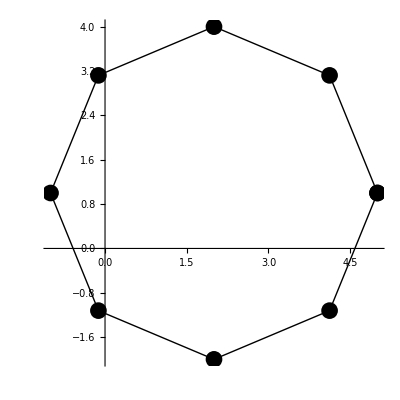

```mathematica
pad=2+I+3cPath[8];
cPlotPath[pad,AxesOrigin->{0,0}]
```

```mathematica
f[z_]:=(z-2-2I)/((z-1)(z-2)(z-3))
g[z_]:=1/f[z]
1/(2π I)cContourIntegral[f'[z]/f[z],z,pad]
1/(2π I)cContourIntegral[g'[z]/g[z],z,pad]
Residue[f[z],{z,1}]
Residue[f[z],{z,2}]
Residue[f[z],{z,3}]
```

-2

2

-1/2-ⅈ

2 ⅈ

1/2-ⅈ

```mathematica
ClearAll[f]
f[z_]:=WeierstrassP[z,WeierstrassInvariants[{1,I}]]
Integrate[z f'[z]/f[z],{z,2,2+I}]-Integrate[z f'[z]/f[z],{z,0,2+I}]//N
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {2.+1.6307264337491272247061977852624818327001639744350376180560574377×10^-29 ⅈ}. NIntegrate obtained -597.21-1.5708 ⅈ and 92.9891 for the integral and error estimates.

-594.069-6.28319 ⅈ

```mathematica
ClearAll[f]
Integrate[f'[z]/f[z],z]
D[Log[f[z]],{z,1}]
```

Log[f[z]]

f'[z]/f[z]

### MFDS 1.3

### MFDS 1.4

### MFDS 1.5

### MFDS 1.6

### MFDS 1.7

```mathematica
Discriminant[4 x^3-a x-b,x,Method->"Modular"]
Discriminant[4 x^3-a x-b,x]/16
```

16 (a^3-27 b^2)

a^3-27 b^2

```mathematica
p=Solve[4 x^3-a x-b==0,x][[1,1,2]];
q=Solve[4 x^3-a x-b==0,x][[2,1,2]];
r=Solve[4 x^3-a x-b==0,x][[3,1,2]];
16((q-p)(r-q)(r-p))^2//FullSimplify
```

a^3-27 b^2

### MFDS 1.8

#### a)

```mathematica
ClearAll[w,p,wi];
w={2,1+3I};
wi=WeierstrassInvariants[w]//N//Chop;
p[z_]:=WeierstrassP[z,wi]
```

```mathematica
p''[w[[1]]]//N
6 WeierstrassE1[wi]^2-1/2 wi[[1]]//N//Chop
```

0.761992

0.761992

```mathematica
ClearAll[e1,e2,e3];
e1=WeierstrassE1[wi]//N;
e2=WeierstrassE2[wi]//N;
e3=WeierstrassE3[wi]//N;
```

```mathematica
p''[w[[1]]]//N//Chop
6 e1^2-1/2 wi[[1]]//N//Chop
6 e1^2+2(e1 e2+e1 e3+e2 e3)//N//Chop
2(e1-e2)(e1-e3)//N//Chop
```

0.761992

0.761992

0.761992

«1 more identical outputs»

```mathematica
6 e1^2-1/2 wi[[1]]//N//Chop
6 e1^2+2(e1 e2+e1 e3+e2 e3)//N//Chop
6 e1^2 +2e1 e3 +2e1 e2+2e2 e3//N//Chop
6 e1^2 +2e1 e3 +2e2 (e1+e3)//N//Chop
6 e1^2 +2e1 e3 -2 e2^2//N//Chop
6 e1^2 -2 e1^2-2e1(-e1-e3) -2 e2^2//N//Chop
6 e1^2 -2 e1^2-2e1 e2 -2 e2^2//N//Chop
6 e1^2+2e1 e2 -2 e1^2-4e1 e2 -2 e2^2//N//Chop
6 e1^2+2e1 e2 -2(-e1-e2)^2//N//Chop
4 e1^2+2 e1^2+2e1 e2 -2(-e1-e2)^2//N//Chop
4 e1^2-2e1 (-e1-e2) -2 e3^2//N//Chop
4 e1^2-2e1 e3 -2 e3^2//N//Chop
2(2e1+e3)(e1-e3)//N//Chop
2(e1-e2)(e1-e3)//N//Chop
```

0.761992

0.761992

0.761992

«11 more identical outputs»

#### b)

```mathematica
ClearAll[e1,e2,e3];
e1=WeierstrassE1[wi]//N;
e2=WeierstrassE2[wi]//N;
e3=WeierstrassE3[wi]//N;
```

```mathematica
p''[w[[1]]+w[[2]]]//N//Chop
6 e2^2-1/2 wi[[1]]//N//Chop
6 e2^2+2(e1 e2+e1 e3+e2 e3)//N//Chop
2(e2-e1)(e2-e3)//N//Chop
```

-0.101763

-0.101763

-0.101763

«1 more identical outputs»

```mathematica
p''[w[[2]]]//N//Chop
6 e3^2-1/2 wi[[1]]//N//Chop
6 e3^2+2(e1 e2+e1 e3+e2 e3)//N//Chop
2(e3-e1)(e3-e2)//N//Chop
```

0.117495

0.117495

0.117495

«1 more identical outputs»

### MFDS 1.9

```mathematica
ClearAll[w,p,wi];
w={2,1+3I};
wi=WeierstrassInvariants[w]//N//Chop;
g2=WeierstrassInvariantG2[w]//N//Chop;
g3=WeierstrassInvariantG3[w]//N//Chop;
p[z_]:=WeierstrassP[z,wi]
v=0.6+0.2I;
```

```mathematica
p[2v]//N
((p[v]^2+1/4 g2)^2+2g3 p[v])/(4 p[v]^3-g2 p[v]-g3)
1/4(p''[v]/p'[v])^2-2p[v]
1/4((12 p[v]^2-g2)/(2p'[v]))^2-2p[v]
```

0.533285-0.343917 ⅈ

0.533285-0.343917 ⅈ

0.533285-0.343917 ⅈ

«1 more identical outputs»

```mathematica
p[2v]
1/4(p''[v]/p'[v])^2-2p[v]
1/4((6 p[v]^2-1/2 g2)^2)/(4 p[v]^3-g2 p[v]-g3)-2p[v]
1/4(((6 p[v]^2-1/2 g2)^2-4 2p[v](4 p[v]^3-g2 p[v]-g3))/(4 p[v]^3-g2 p[v]-g3))
1/4(((6 p[v]^2-1/2 g2)^2-32 p[v]^4+8g2 p[v]^2+8g3 p[v])/(4 p[v]^3-g2 p[v]-g3))
1/4((36 p[v]^4-6g2 p[v]^2+1/4 g2^2-32 p[v]^4+8g2 p[v]^2+8g3 p[v])/(4 p[v]^3-g2 p[v]-g3))
(9 p[v]^4-3/2 g2 p[v]^2+1/16 g2^2-8 p[v]^4+2g2 p[v]^2+2g3 p[v])/(4 p[v]^3-g2 p[v]-g3)
(p[v]^4+1/2 g2 p[v]^2+1/16 g2^2+2g3 p[v])/(4 p[v]^3-g2 p[v]-g3)


((p[v]^2+1/4 g2)^2+2g3 p[v])/(4 p[v]^3-g2 p[v]-g3)
```

0.533285-0.343917 ⅈ

0.533285-0.343917 ⅈ

0.533285-0.343917 ⅈ

«6 more identical outputs»

### MFDS 1.10

```mathematica
ClearAll[f]
RSolve[f[x+ω]==A f[x],f[x],x]
```

{{f[x]→A^(-1+x/ω) C[1]}}

### MFDS 1.11

```mathematica
1/z+Sum[(1/(z+m)-1/m)+(1/(z-m)+1/m),{m,1,Infinity}]//FullSimplify
```

π Cot[π z]

```mathematica
ClearAll[q]
q[z_]:=Exp[2 π ⅈ z]
π ⅈ - 2 π ⅈ Sum[q[z]^m,{m,0,Infinity}]//FullSimplify
```

π Cot[π z]

### MFDS 1.12

### MFDS 1.13

### MFDS 1.14

### MFDS 1.15

2. The Modular Group and Modular Functions

## 2.1 Möbius Transformations

UZT’s

## Yin Yang Symbol

```mathematica
Graphics[Rotate[{Black,Circle[{0,0},1],White,DiskSegment[{0,0},1,{0,π}],
Black,DiskSegment[{0,0},1,{π,2π}],White,Disk[{0.5,0},0.5],
Black,Disk[{-0.5,0},0.5],Black,Disk[{0.5,0},0.125],
White,Disk[{-0.5,0},0.125]
},90  Degree]]//Show
```

-Graphics-

```mathematica
Graphics[{Black,Circle[{0,0},1],White,DiskSegment[{0,0},1,{1/2 π,3/2 π}],
Black,DiskSegment[{0,0},1,{3/2 π,5/2 π}],White,Disk[{0,0.5},0.5],
Black,Disk[{0,-0.5},0.5],Black,Disk[{0,0.5},0.125],
White,Disk[{0,-0.5},0.125]
}]//Show
```

-Graphics-

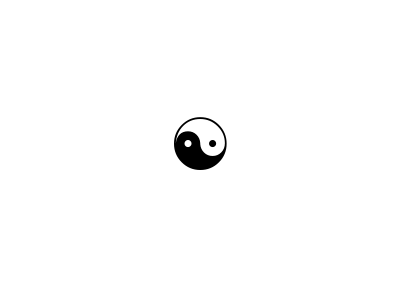

```mathematica
Graphics[Text[Style["☯",288]],Method->"ShrinkWrap"->True]
```

```mathematica
Style["☯",288]
```

☯

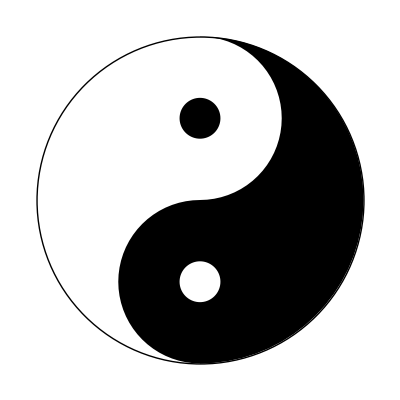

```mathematica
d[y_,r_:1/2,a_:{0,2}]:=Disk[{0,y},r,a π];
p={{0,2,{1,3}},{0,2,{3,5}},{1},{-1},{-1,1/4},{1,1/4}}/2;
Graphics@{Riffle[d@@@p,{White,Black},{1,-1,2}],Circle[]}
```

```mathematica
ClearAll[ls]
ls=Table[{5,k},{k,0,5}]
Union[Map[#[[1]]+#[[2]]I&,ls],Rest[Map[#[[1]]I+#[[2]]&,ls]]]
ls=AppendTo[ls,ls];
```

## Curves

```mathematica
ClearAll[a,b,c];
a=0.65;
b=0.85;
c=0.04;
Manipulate[PolarPlot[c √((a^2 Sin[t]^2-b^2 Cos[t]^2)/(Sin[t]^2-Cos[t]^2)),{t,0,s π},Axes->False],{{a,0.05},0,1},{{b,0.1},0,1},{{c,0.4},0,1},{{s,2},2,24}]
```

## tmp-1: Various stuff to sort out

### tmp-1

```mathematica
g[fun_]:={FunctionInjective[fun[x],x],FunctionSurjective[fun[x],x],FunctionBijective[fun[x],x]}
```

```mathematica
g[Sin]
g[Tan]
g[Exp]
g[#^3&]
```

{False,False,False}

{False,True,False}

{True,False,False}

{True,True,True}

```mathematica
f[x_,y_]:=x^2+y/;{x,y}≠{2,2}
Sum[f[j,k],{j,1,3},{k,1,3}]-f[2,2]
```

54

```mathematica
WeierstrassP[.2+.3I,{1,I}]
```

-2.96065-7.09502 ⅈ

```mathematica
f[z_,w1_,w2_]:=1/z^2+
Sum[
1/(z+i w1+ j w2)^2-1/(i w1+ j w2)^2+
1/(z+i w1- j w2)^2-1/(i w1- j w2)^2+
1/(z-i w1+ j w2)^2-1/(i w1+ j w2)^2+
1/(z-i w1+ j w2)^2-1/(i w1- j w2)^2,
{i,1,k},{j,1,k}
]+Sum[
1/(z+i w1+ j w2)^2-1/(i w1+ j w2)^2+
1/(z+i w1- j w2)^2-1/(i w1- j w2)^2,
{i,0,0},{j,1,k}
]+Sum[
1/(z+i w1+ j w2)^2-1/(i w1+ j w2)^2+
1/(z+i w1- j w2)^2-1/(i w1- j w2)^2,
{i,1,k},{j,0,0}
]/;{w1,w2}≠{0,0}
```

```mathematica
k=10;
f[.2+.3I,2,2I]
k=1000;
f[.2+.3I,2,2I]
```

-3.16452-5.99215 ⅈ

-3.16886-3.71288 ⅈ

```mathematica
WeierstrassP[.2+.3I,{1,I}]
f[z_,w1_,w2_]:=1/z^2+
Sum[
1/(z+i w1+ j w2)^2-1/(i w1+ j w2)^2+
1/(z+i w1- j w2)^2-1/(i w1- j w2)^2+
1/(z-i w1+ j w2)^2-1/(i w1+ j w2)^2+
1/(z-i w1+ j w2)^2-1/(i w1- j w2)^2,
{i,1,100},{j,1,100}
]/;{w1,w2}≠{0,0}
```

-2.96065-7.09502 ⅈ

```mathematica
f[.2+.3I,1,I]
```

-3.36632+2.11861 ⅈ

```mathematica
1/(2.2+2.3I)^2
```

-0.00438524-0.0986192 ⅈ

```mathematica
WeierstrassP[2.2+2.3I,{2,2I}]
f[z_,w1_,w2_]:=1/z^2+Sum[
Piecewise[{{1/(z+i w1+ j w2)^2-1/(i w1+ j w2)^2,{i,j}≠{0,0}},{0,True}}],
{i,-k,k},{j,-k,k}]/;{w1,w2}≠{0,0}
k=0;
f[2.2+2.3I,2,2I]
k=15;
f[2.2+2.3I,2,2I]
```

-7.53012-12.3981 ⅈ

-0.00438524-0.0986192 ⅈ

-2.98777-7.03242 ⅈ

```mathematica
g[z_,w1_,w2_,i_,j_]:=1/(z+i w1+ j w2)^2-1/(i w1+ j w2)^2
g[.2+.3I,1,I,110050,175]
```

-3.02261×10^-16-4.48734×10^-16 ⅈ

```mathematica
Series[WeierstrassP[z,WeierstrassInvariants[{1,I}]],{z,0,20}]//Normal
```

1/z^2+(z^2 Gamma[1/4]^8)/(5120 π^2)+(z^6 Gamma[1/4]^16)/(78643200 π^4)+(z^10 Gamma[1/4]^24)/(2617245696000 π^6)+(z^14 Gamma[1/4]^32)/(91122026151936000 π^8)+(z^18 Gamma[1/4]^40)/(3499085804234342400000 π^10)

```mathematica
g[z_]:=1/z^2+(z^2 Gamma[1/4]^8)/(5120 π^2)+(z^6 Gamma[1/4]^16)/(78643200 π^4)+(z^10 Gamma[1/4]^24)/(2617245696000 π^6)+(z^14 Gamma[1/4]^32)/(91122026151936000 π^8)+(z^18 Gamma[1/4]^40)/(3499085804234342400000 π^10)
g[z_]:=1/z^2+(z^2 Gamma[1/4]^8)/(5120 π^2)+(z^6 Gamma[1/4]^16)/(78643200 π^4)
```

```mathematica
WeierstrassP[0.05+0.05I,{6,111I}]
WeierstrassP[0.05+0.05I,{6,101I}]
WeierstrassP[0.05+0.05I,{2,2I}]
g[0.05+0.05I]
```

2.44249×10^-14-199.999 ⅈ

-2.44249×10^-14-199.999 ⅈ

6.43929×10^-15-200. ⅈ

8.3268×10^-15-199.997 ⅈ

```mathematica
WeierstrassP[1+I, WeierstrassInvariants[{1, I}]]//N//Chop
```

0

```mathematica
DSolve[{y''[x]==x  y[x]}, y[x], x]
```

{{y[x]→AiryAi[x] C[1]+AiryBi[x] C[2]}}

```mathematica
f[z_]:=Sin[z]/z
g[w_]:=(Series[f[z],{z,0,18}]//Normal)/.z:> w
h[w_]:=Sinc[w]
```

```mathematica
f[0.1]//N
g[0.1]//N
h[0.1]//N
Limit[f[z],z->0]
```

0.998334

0.998334

0.998334

1

```mathematica
Series[Sin[z]/z,{z,0,6}]
Series[Sinc[z],{z,0,6}]
```

1-z^2/6+z^4/120-z^6/5040+O[z]^7

1-z^2/6+z^4/120-z^6/5040+O[z]^7

```mathematica
(Series[ⅇ^(1/z),{z,Infinity,12}]//Normal)
```

1+1/(479001600 z^12)+1/(39916800 z^11)+1/(3628800 z^10)+1/(362880 z^9)+1/(40320 z^8)+1/(5040 z^7)+1/(720 z^6)+1/(120 z^5)+1/(24 z^4)+1/(6 z^3)+1/(2 z^2)+1/z

```mathematica
Residue[1/(z-1),{z,1}]
```

1

```mathematica
f[z_]:=ⅇ^(1/z)
f[.1+.1I]
f[.01+.1I]
f[.001+.1I]
f[.0001+.0001I]
f[.0001+.001I]
```

42.0992+142.317 ⅈ

-2.39204+1.23383 ⅈ

-0.927909+0.600303 ⅈ

4.58998352293687×10^2170+2.93191724614707×10^2171 ⅈ

-8.77757×10^42+4.76476×10^42 ⅈ

```mathematica
Integrate[Sin[x]/x,{x,0,Infinity}]
Integrate[Sin[x]/x,{x,-Infinity,Infinity}]
```

π/2

π

```mathematica
Log[1]
```

0

```mathematica
ⅇ^(1+(1+2π )I)//N
ⅇ^(1+(1+12π )I)//N
ⅇ^(1+(1+26π )I)//N
```

1.46869+2.28736 ⅈ

1.46869+2.28736 ⅈ

1.46869+2.28736 ⅈ

```mathematica
Log[1.4686939399158856+1+(1+26π )I]//N
```

4.41544+1.54095 ⅈ

```mathematica
Exp[Log[1/2+3I]-80 π I]//FullSimplify
```

1/2+3 ⅈ

```mathematica
FunctionAnalytic[Log[z],z,Complexes]
```

False

```mathematica
11.07/π
```

3.52369

```mathematica
Log[1]
```

0

```mathematica
f[t_]:=Log[4+ⅇ^(I t)]
f[0.]
f[6 π]//N
f[16 π]//N
```

1.60944+0. ⅈ

1.60944

1.60944

```mathematica
Series[1/(z-1),{z,Infinity,6}]
Series[1/(1-1/2 z),{z,0,6}]
```

1/z+(1/z)^2+(1/z)^3+(1/z)^4+(1/z)^5+(1/z)^6+O[1/z]^7

1+z/2+z^2/4+z^3/8+z^4/16+z^5/32+z^6/64+O[z]^7

```mathematica
1/(z-1)+1/(1-1/2 z)//Factor
```

-z/((-2+z) (-1+z))

```mathematica
Series[z ⅇ^(1/z),{z,Infinity,12}]
```

z+1+1/(2 z)+1/(6 z^2)+1/(24 z^3)+1/(120 z^4)+1/(720 z^5)+1/(5040 z^6)+1/(40320 z^7)+1/(362880 z^8)+1/(3628800 z^9)+1/(39916800 z^10)+1/(479001600 z^11)+1/(6227020800 z^12)+O[1/z]^13

```mathematica
Apart[1/((z-1)(z-2)),z]
```

1/(-2+z)-1/(-1+z)

```mathematica
Series[ⅇ^(1/z),{z,Infinity,12}]
```

1+1/z+1/(2 z^2)+1/(6 z^3)+1/(24 z^4)+1/(120 z^5)+1/(720 z^6)+1/(5040 z^7)+1/(40320 z^8)+1/(362880 z^9)+1/(3628800 z^10)+1/(39916800 z^11)+1/(479001600 z^12)+O[1/z]^13

```mathematica
Series[1/((z-1)(z-2)),{z,0,4}]
```

1/2+(3 z)/4+(7 z^2)/8+(15 z^3)/16+(31 z^4)/32+O[z]^5

```mathematica
(Series[1/(z-2),{z,0,4}]//Normal)-(Series[1/(z-1),{z,0,4}]//Normal)
```

1/2+(3 z)/4+(7 z^2)/8+(15 z^3)/16+(31 z^4)/32

```mathematica
Series[1/(z-2),{z,0,4}]//Normal
```

-1/2-z/4-z^2/8-z^3/16-z^4/32

```mathematica
Series[1/(z-1),{z,Infinity,12}]//Normal
```

1/z^12+1/z^11+1/z^10+1/z^9+1/z^8+1/z^7+1/z^6+1/z^5+1/z^4+1/z^3+1/z^2+1/z

```mathematica
Apart[1/(z(z-1)),z]
```

1/(-1+z)-1/z

```mathematica
Series[1/(z(z-1)),{z,0,6}]
```

-1/z-1-z-z^2-z^3-z^4-z^5-z^6+O[z]^7

```mathematica
Series[1/(z(z-1)),{z,Infinity,6}]
```

(1/z)^2+(1/z)^3+(1/z)^4+(1/z)^5+(1/z)^6+O[1/z]^7

```mathematica
DSolve[{-y[t]==x'[t],x[t]==y'[t]},{y[t],x[t]},t]
```

{{x[t]→C[1] Cos[t]-C[2] Sin[t],y[t]→C[2] Cos[t]+C[1] Sin[t]}}

```mathematica
m:={{4,-1},{0,0.25}}
m.{{1+0.5I},{0.5-2I}}//mf
```

(3.5+4. ⅈ
0.125-0.5 ⅈ)

```mathematica
Orthogonalize[{{3/2,1},{-2,-1/2}}]
```

{{3/(√13),2/(√13)},{-2/(√13),3/(√13)}}

```mathematica
{3/2,1}.{-2,-1/2}
```

-7/2

```mathematica
{3/(√13),2/(√13)}.{-2/(√13),3/(√13)}
```

0

```mathematica
(3/(√13))^2+(2/(√13))^2
```

1

### tmp-2

```mathematica
rr=3;
torus[u_,v_]:={(rr+Cos[2 Pi u]) Cos[2 Pi v],(rr+Cos[2 Pi u]) Sin[2 Pi v],Sin[2 Pi u]}
tor=ParametricPlot3D[torus[u,v],{u,0,1},{v,0,1},Boxed->False,MeshStyle->None];
knt=ParametricPlot3D[torus[1,u],{u,0,1},Boxed->False,Axes->False];
grp0=Graphics3D[{Blue,Cylinder[],Red,Sphere[{0,0,2}],Black,Thick,Dashed,Line[{{-2,0,2},{2,0,2},{0,0,4},{-2,0,2}}],Yellow,Polygon[{{-3,-3,-2},{-3,3,-2},{3,3,-2},{3,-3,-2}}],Green,Opacity[.3],Cuboid[{-2,-2,-2},{2,2,-1}]}];
grp1=Graphics3D[{PointSize[0.02],Point[{0,4,0.5}]}];
Show[tor,knt,grp1]
```

-Graphics3D-

```mathematica
Show[knt,grp1]
```

-Graphics3D-

### tmp-3

```mathematica
p[z_]:=WeierstrassP[z,WeierstrassInvariants[{1,I}]]
p[5.35]//N//Chop
p[5.35+17(2+2I)]//N//Chop
```

2.62542

2.62542

```mathematica
123
```

123

```mathematica
Solve[WeierstrassP[1.4+0.6I,WeierstrassInvariants[{1,I}]]==WeierstrassP[x,WeierstrassInvariants[{1,I}]],x]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::incs: Warning: Solve was unable to prove that the solution set found is complete.

{{x→ConditionalExpression[(0.6+1.4 ⅈ)+2. C[1]+(0.+2. ⅈ) C[2], (C[1]|C[2])∈ℤ]},{x→ConditionalExpression[(1.4+0.6 ⅈ)+2. C[1]+(0.+2. ⅈ) C[2], (C[1]|C[2])∈ℤ]}}

```mathematica
WeierstrassP[1.4+0.6I,WeierstrassInvariants[{1,I}]]//Chop

WeierstrassP[0.6+1.4I,WeierstrassInvariants[{1,I}]]//Chop
WeierstrassP[4.6+3.4I,WeierstrassInvariants[{1,I}]]//Chop
WeierstrassP[3.4+2.6I,WeierstrassInvariants[{1,I}]]//Chop
```

((1.77636×10^-15+1.00495 ⅈ) Chop)[((-1.59872×10^-14+1.00495 ⅈ) Chop)[((-9.54792×10^-15+1.00495 ⅈ) Chop)[0.+1.00495 ⅈ]]]

```mathematica
((1.5+1.4I+3000(2+2I))+(0.5+0.6I+111(2+2I)))/(2+2I)
```

3112.+0. ⅈ

```mathematica
WeierstrassP[7.25+10.5I,WeierstrassInvariants[{1,I}]]//N
WeierstrassP[1.25+4.5I,WeierstrassInvariants[{1,I}]]//N
```

0.603561+0.717759 ⅈ

0.603561+0.717759 ⅈ

```mathematica
ClearAll[f]
f[x_]:=WeierstrassP[x,WeierstrassInvariants[{1,I}]]
u=1.2+1.2I
v=0.3+0.7I
f[u+v]-f[u-v]//N
-(f'[u]f'[v])/(f[u]-f[v])^2//N
f[.75+.85I]//N
f[1.25+1.15I]//N
```

1.2+1.2 ⅈ

0.3+0.7 ⅈ

2.99571-1.15055 ⅈ

2.99571-1.15055 ⅈ

-0.119239-0.221675 ⅈ

-0.119239-0.221675 ⅈ

```mathematica
ClearAll[f]
DSolve[f'[x]==√q[f[x]],f[x],x]
```

$Aborted

### tmp-4

```mathematica
ClearAll[f]
f[x_]:=WeierstrassP[x,WeierstrassInvariants[{4,4I}]]
g[x_]:=WeierstrassPPrime[x,WeierstrassInvariants[{4,4I}]]^3
h[x_]:=WeierstrassPPrime[x,WeierstrassInvariants[{4,4I}]]

g[2.2+1.3I]//Chop;
-g[-(2.2+1.3I)]//Chop;
g[1.8+2.7I]g[1.8+2.7I]//Chop;
g[-(1.8+2.7I)]g[-(1.8+2.7I)]//Chop;


R[z_]:=(g[z]+g[-z])/2
S[z_]:=((g[z]-g[-z])/2)/h[z]
T[z_]:=R[z]+h[z]S[z]

u=1.8+2.7I;
g[u]//Chop
T[u]//Chop
S[u]
S[-u]
T[u]
-T[-u]
```

0.000211434+0.00025694 ⅈ

0.000211434+0.00025694 ⅈ

0.00399497+0.00266427 ⅈ

0.00399497+0.00266427 ⅈ

0.000211434+0.00025694 ⅈ

0.000211434+0.00025694 ⅈ

```mathematica
ComplexPlot3D[g[z],{z,0,4+4I}]
```

-Graphics3D-

```mathematica
ComplexPlot[g[z],{z,0,8+8I},Frame->False]
```

-Graphics-

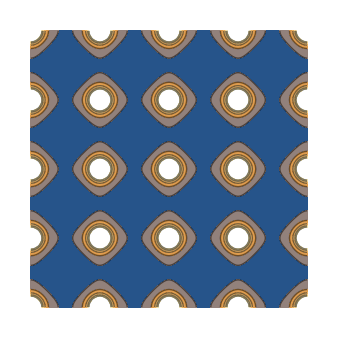

```mathematica
ComplexContourPlot[Abs[p[z]],{z,0,8+8I},Frame->False]
```

```mathematica
ColorData["Gradients"]//tf;
```

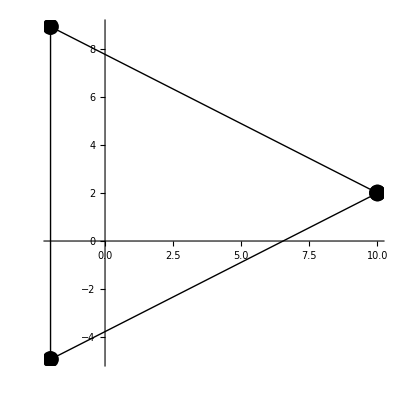

```mathematica
pad=2+2I+8cPath[3];
cPlotPath[pad,AxesOrigin->{0,0}]
```

```mathematica
1/(2π I)cContourIntegral[g'[z]/g[z],z,pad]//N
```

-5.23025×10^-15-6.40528×10^-15 ⅈ

```mathematica
p[z_]:=WeierstrassP[z,WeierstrassInvariants[{1,I}]]
q[z_]:=(p[z]-p[3+3I])/(p[z]-p[2+2I])
r[a_]:=p[a]/q[a]
```

```mathematica
r[1.2]//Abs
r[1.3]//Abs
r[1.4]//Abs
r[3.5+7.25I]//Abs
```

6.42775×10^60

6.42775×10^60

6.42775×10^60

«1 more identical outputs»

### tmp-5

```mathematica
p[z_]:=WeierstrassP[z,WeierstrassInvariants[{1,I}]]
```

```mathematica
p''[1.]
```

11.817

```mathematica
Series[Exp[-1/z],{z,Infinity,10}]
```

1-1/z+1/(2 z^2)-1/(6 z^3)+1/(24 z^4)-1/(120 z^5)+1/(720 z^6)-1/(5040 z^7)+1/(40320 z^8)-1/(362880 z^9)+1/(3628800 z^10)+O[1/z]^11

```mathematica
Accumulate[Table[(n+2)^2-n^2,{n,1,401,2}]]//Total
Accumulate[Table[4n+4,{n,1,401,2}]]//Total
```

10989608

10989608

```mathematica
Table[{k,BaseForm[k,5]},{k,1,25}]
```

{{1,1_5},{2,2_5},{3,3_5},{4,4_5},{5,10_5},{6,11_5},{7,12_5},{8,13_5},{9,14_5},{10,20_5},{11,21_5},{12,22_5},{13,23_5},{14,24_5},{15,30_5},{16,31_5},{17,32_5},{18,33_5},{19,34_5},{20,40_5},{21,41_5},{22,42_5},{23,43_5},{24,44_5},{25,100_5}}

```mathematica
ClearAll[f]
f[n_]:={n,Ceiling[(√(n+1)-1)/2],8Ceiling[(√(n+1)-1)/2],8(Ceiling[(√(n+1)-1)/2]-Floor[(√(n+1)-1)/2]),(√(n+1)-1)/2}
Table[f[k],{k,1,49}]//tf
```

1 | 1 | 8 | 8 | 1/2 (-1+√2)
2 | 1 | 8 | 8 | 1/2 (-1+√3)
3 | 1 | 8 | 8 | 1/2
4 | 1 | 8 | 8 | 1/2 (-1+√5)
5 | 1 | 8 | 8 | 1/2 (-1+√6)
6 | 1 | 8 | 8 | 1/2 (-1+√7)
7 | 1 | 8 | 8 | 1/2 (-1+2 √2)
8 | 1 | 8 | 0 | 1
9 | 2 | 16 | 8 | 1/2 (-1+√10)
10 | 2 | 16 | 8 | 1/2 (-1+√11)
11 | 2 | 16 | 8 | 1/2 (-1+2 √3)
12 | 2 | 16 | 8 | 1/2 (-1+√13)
13 | 2 | 16 | 8 | 1/2 (-1+√14)
14 | 2 | 16 | 8 | 1/2 (-1+√15)
15 | 2 | 16 | 8 | 3/2
16 | 2 | 16 | 8 | 1/2 (-1+√17)
17 | 2 | 16 | 8 | 1/2 (-1+3 √2)
18 | 2 | 16 | 8 | 1/2 (-1+√19)
19 | 2 | 16 | 8 | 1/2 (-1+2 √5)
20 | 2 | 16 | 8 | 1/2 (-1+√21)
21 | 2 | 16 | 8 | 1/2 (-1+√22)
22 | 2 | 16 | 8 | 1/2 (-1+√23)
23 | 2 | 16 | 8 | 1/2 (-1+2 √6)
24 | 2 | 16 | 0 | 2
25 | 3 | 24 | 8 | 1/2 (-1+√26)
26 | 3 | 24 | 8 | 1/2 (-1+3 √3)
27 | 3 | 24 | 8 | 1/2 (-1+2 √7)
28 | 3 | 24 | 8 | 1/2 (-1+√29)
29 | 3 | 24 | 8 | 1/2 (-1+√30)
30 | 3 | 24 | 8 | 1/2 (-1+√31)
31 | 3 | 24 | 8 | 1/2 (-1+4 √2)
32 | 3 | 24 | 8 | 1/2 (-1+√33)
33 | 3 | 24 | 8 | 1/2 (-1+√34)
34 | 3 | 24 | 8 | 1/2 (-1+√35)
35 | 3 | 24 | 8 | 5/2
36 | 3 | 24 | 8 | 1/2 (-1+√37)
37 | 3 | 24 | 8 | 1/2 (-1+√38)
38 | 3 | 24 | 8 | 1/2 (-1+√39)
39 | 3 | 24 | 8 | 1/2 (-1+2 √10)
40 | 3 | 24 | 8 | 1/2 (-1+√41)
41 | 3 | 24 | 8 | 1/2 (-1+√42)
42 | 3 | 24 | 8 | 1/2 (-1+√43)
43 | 3 | 24 | 8 | 1/2 (-1+2 √11)
44 | 3 | 24 | 8 | 1/2 (-1+3 √5)
45 | 3 | 24 | 8 | 1/2 (-1+√46)
46 | 3 | 24 | 8 | 1/2 (-1+√47)
47 | 3 | 24 | 8 | 1/2 (-1+4 √3)
48 | 3 | 24 | 0 | 3
49 | 4 | 32 | 8 | 1/2 (-1+5 √2)

```mathematica
Sum[(MoebiusMu[n] x^n)/(1-x^n),{n,1,Infinity}]
```

x

```mathematica
10^22/2.
```

5.×10^21

```mathematica
IntegerPartitions[19]//Length
```

490

## tmp-2: makeEllipticFunction ( TBD: WeierstrassSigma -> EllipticTheta )

```mathematica
ClearAll[makeEllipticFunction]
makeEllipticFunction[z_,{ω1_,ω3_},zeros_?VectorQ,poles_?VectorQ]:=Module[
{c=π/(2 ω1),q=Exp[I π ω3/ω1]},
(Product[EllipticTheta[1,c (z-r),q],{r,zeros}]/Product[EllipticTheta[1,c (z-s),q],{s,poles}])(EllipticTheta[1,c (z-Last[poles]),q]/EllipticTheta[1,c (z-Last[poles]-(Total[zeros]-Total[poles])),q])]/;Length[zeros]==Length[poles]&&With[{wl={ω1,ω3,Total[zeros]-Total[poles]}},PossibleZeroQ[wl.FindIntegerNullVector[wl]]]
```

```mathematica
makeEllipticFunction[z_, {ω1_, ω3_}, zeros_List,poles_List]:=Module[{g2,g3,σ},
{g2,g3}=WeierstrassInvariants[N[{ω1,ω3}]];σ=WeierstrassSigma[#,{g2,g3}]&;(Times @@σ[z-zeros])/(Times @@σ[z-poles])σ[z-Last[poles]]/σ[z-Last[poles]-(Total[zeros]-Total[poles])]]/;Length[zeros]==Length[poles]&&Resolve[Exists[{μ,ν},Element[{μ,ν},Integers],Total[zeros]-Total[poles]==μ ω1+ν ω3]]
```

```mathematica
f[z_]=makeEllipticFunction[z,{1,I},{1/4+1/4 I,1/4+1/4 I,-1/2-1/2 I},{0,0,0}] // Chop;

f[z_]=makeEllipticFunction[z,{1,I},{
1/4+1/4 I,
1/4+1/4 I,
-1/2-1/2 I,
1/10+2/10I,
1/10+2/10I,
-2/10-4/10I
},{0,0,0,0,0,0}] // Chop
```

(EllipticTheta[1,1/2 π ((-1/4-ⅈ/4)+z),ⅇ^-π]^2 EllipticTheta[1,1/2 π ((-1/10-ⅈ/5)+z),ⅇ^-π]^2 EllipticTheta[1,1/2 π ((1/5+(2 ⅈ)/5)+z),ⅇ^-π] EllipticTheta[1,1/2 π ((1/2+ⅈ/2)+z),ⅇ^-π])/(EllipticTheta[1,(π z)/2,ⅇ^-π]^6)

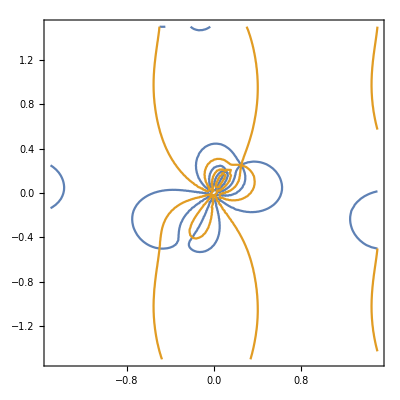

```mathematica
ContourPlot[Evaluate[{Re[f[x+I y]]==0,Im[f[x+I y]]==0}],{x,-1.5,1.5},{y,-1.5,1.5}]
```

```mathematica
ComplexPlot[f[z],{z,-(2+2I),(2+2I)}]
```

-Graphics-

```mathematica
ComplexPlot3D[f[z],{z,-(2+2I),(2+2I)}]
```

-Graphics3D-

## UZT-1: Are both Sums equal ?

```mathematica
Sum[1/(n+τ)^k,{n,-Infinity,Infinity},Assumptions->{k≥2}]//FullSimplify
```

(-1)^-k HurwitzZeta[k,1-τ]+HurwitzZeta[k,τ]

```mathematica
(-2 π ⅈ)^k/((k-1)!)Sum[m^(k-1)ⅇ^(2 π ⅈ τ m),{m,1,Infinity}]
```

((-2 ⅈ π)^k PolyLog[1-k,ⅇ^(2 ⅈ π τ)])/((-1+k)!)

## UZT-2:

```mathematica
ClearAll[q,f1,f2,k]
q[z_]:=Exp[2 π ⅈ z]
f1[z_,k_]:=Sum[n^(2k-1)q[z]^n/(1-q[z]^n),{n,1,Infinity}]
f2[z_,k_]:=Sum[DivisorSigma[k,n]q[z],{n,1,Infinity}]
f1[0.5I,4]//N
f2[0.5I,4]//N
```

0.532143

NumericalMath`NSequenceLimit::seqlim: The general form of the sequence could not be determined, and the result may be incorrect.

800.601

```mathematica
ClearAll[f1,f2,n,k,x]
f1[k_,x_]:=Sum[n^k x^n/(1-x^n),{n,1,Infinity}]
f2[k_,x_]:=Sum[DivisorSigma[k,n] x^n,{n,1,Infinity}]
```

```mathematica
f1[3,0.6]//N
f2[3,0.6]//N
f1[7,0.16]//N
f2[7,0.16]//N
```

95.3671

95.3671

39.7804

39.7804

## UZT-3: Bouw nSumPrime

```mathematica
SetAttributes[nSumPrime,HoldAll]
(*nSumPrime[f_[a___,var_,b___],{var_,xmin_,xmax_}]:=ListPlot[Table[{y,f[a,y,b]},{y,xmin,xmax,(xmax-xmin)/100}]]*)
nSumPrime[f_[var_]]:=Sum[f[var]+f[-var],{var,1,Infinity}]

g1[m_]:=(1/(z+m)-1/m)
1/z+nSumPrime[g1[n]]//FullSimplify
```

π Cot[π z]